```mathematica
Aphi0=(1-Cos[h])
Aphi0=Sin[h]^2
Aphi2=Cos[h]*Sin[h]^2
Aphi4=Cos[h]^3*Sin[h]
Integrate[Aphi0*Aphi2,{h,0,Pi/2}]
```

1-Cos[h]

Sin[h]^2

Cos[h] Sin[h]^2

Cos[h]^3 Sin[h]

1/5

```mathematica
Aphi4=(5*Cos[h]^3*Sin[h]-Sin[h])*Sin[h]
Aphi4=(5*Cos[h]^2*Sin[h]-Sin[h])*Sin[h]
Br=D[Aphi4,h]/(Sin[h])
Series[Br,{h,0,1}]
```

Sin[h] (-Sin[h]+5 Cos[h]^3 Sin[h])

Sin[h] (-Sin[h]+5 Cos[h]^2 Sin[h])

Csc[h] (Cos[h] (-Sin[h]+5 Cos[h]^2 Sin[h])+Sin[h] (-Cos[h]+5 Cos[h]^3-10 Cos[h] Sin[h]^2))

8+O[h]^2

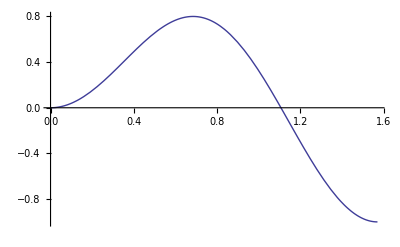

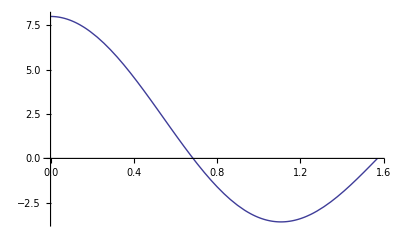

```mathematica
Plot[Aphi4,{h,0,Pi/2}]
Plot[Br,{h,0,Pi/2}]
```

-5/4 Cos[h] (1+7 Cos[2 h]) Sin[h]^2

1/48 (17+40 Cos[2 h]-105 Cos[4 h]+15 (9 Cos[h]+7 Cos[3 h]) Log[Tan[h/2]^2] Sin[h]^2)

Csc[h] (-5/2 Cos[h]^2 (1+7 Cos[2 h]) Sin[h]+5/4 (1+7 Cos[2 h]) Sin[h]^3+35/2 Cos[h] Sin[h]^2 Sin[2 h])

-20+O[h]^2

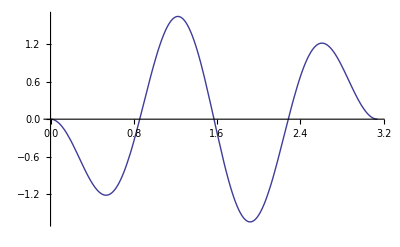

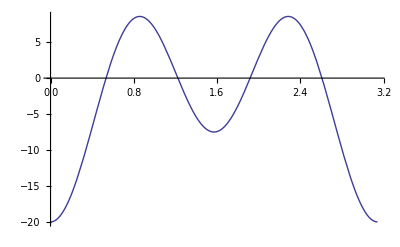

```mathematica
l=-1/2;
l=4;tryit=FullSimplify[Abs[Sin[h]]*LegendreP[l,1,Cos[h]],{h>0}]
FullSimplify[Abs[Sin[h]]*LegendreQ[l,1,Cos[h]],{h>0}]
god=D[tryit,h]/Sin[h]
Series[god,{h,0,1}]
Plot[tryit,{h,0,Pi}]
Plot[god,{h,0,Pi}]
```

```mathematica
saphi0=(1-Cos[h])
saphi2=Sin[h]^2*Cos[h]
coef=0.1
saphi4=(20*Sin[h]^2*((1-coef)*Cos[h]^5+coef*Cos[h]))
sBr=D[saphi4,h]/Sin[h]
Series[sBr,{h,0,2}]
```

1-Cos[h]

Cos[h] Sin[h]^2

0.1

20 (0.1 Cos[h]+0.9 Cos[h]^5) Sin[h]^2

Csc[h] (40 Cos[h] (0.1 Cos[h]+0.9 Cos[h]^5) Sin[h]+20 Sin[h]^2 (-0.1 Sin[h]-4.5 Cos[h]^4 Sin[h]))

40.-204. h^2+O[h]^3

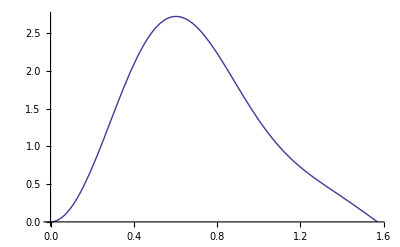

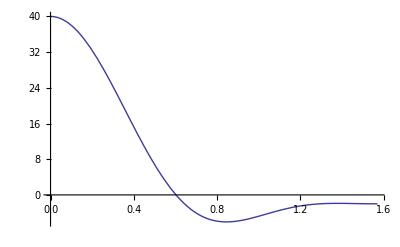

```mathematica
Plot[saphi4,{h,0,Pi/2}]
Plot[sBr,{h,0,Pi/2}]
```